## Prel

```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z],Tan[z_]:>Defer@Sin[z]/Defer@Cos[z],Cot[z_]:>Defer@Cos[z]/Defer@Sin[z]}&;rep={kx->kp Cos[ϕ],ky->kp Sin[ϕ],kz-> kz};
rep1={kx->Subscript[k, x],ky->Subscript[k, y],kp->Subscript[k, p],Bx->B,v0->Subscript[v, 0],ηx->Subscript[η, x],ηz->Subscript[η, z],k0->Subscript[k, 0],ηtilde->η̃};
ass=Assumptions->{kp,k0,γ,ηtilde,ϕ,v0,kx,ky,ϵ,η,ηx,ηz,κ,κp,kp,μ,Bx,e,vz,u}∈ Reals && v0>0 && μ>=0 &&μ<k0 v0  && k0>0 &&  κ>0  && k0>κ &&  0<η<=1 && ηtilde>0 &&  0<ηx<=1&&  0<ηz<=1;
```

```mathematica
Clear[v0vecxtilt,v0vecztilt,vomm,Om, v0];
v0vecxtilt=v0{Cos[γ] Cos[ϕ]+ηx, Cos[γ] Sin[ϕ], Sin[γ]};
v0vecztilt=v0{Cos[γ] Cos[ϕ], Cos[γ] Sin[ϕ], Sin[γ]+ηz};
(* -Graphics- *)
Om=-1/(4κ(k0+κ Cos[γ])){Sin[2γ] Cos[ϕ],Sin[2γ] Sin[ϕ],2(Sin[γ])^2};
J=κ(k0+κ Cos[γ]);ηt=η v0 k0;
repk=κ->(μ-ηt Cos[ϕ])/(v0 (1+η Cos[γ]Cos[ϕ]));
repkz=κ->μ/(v0 (1+η Sin[γ]));
Clear[enx,enz];
enx=v0 κ(1+ηx Cos[γ]Cos[ϕ])+ηtilde Cos[ϕ];
enz=v0 κ(1+ηz  Sin[γ]);
facx(* = 1/D[enx,κ] *)=1/(v0(1+η Cos[γ](* ηx Cos[ϕ]*)));
facz(* = 1/D[enz,κ]*)=1/(v0(1+ ηz Sin[γ]));ηt=v0 k0;
```

#### test

```mathematica
(* test with a given η and ArcCos[μ/ηt] = π/6 *)
inti=(π (-1+√(1-η^2 Cos[ϕ]^2)))/(η^3 Cos[ϕ]^2);
η=1/10;
i1=Integrate[inti,{ϕ,-π ,-π/2 }(*,Assumptions->{η}∈ Reals &&  0<η<1*)]
i2=Integrate[inti,{ϕ,π/2 ,π }(*,Assumptions->{η}∈ Reals &&  0<η<1*)];
i1==i2

i3=FullSimplify[Integrate[inti,{ϕ,-π/2,0 },Assumptions->{η}∈ Reals &&  0<η<1],Assumptions->{η}∈ Reals &&  0<η<1]

i4=FullSimplify[Integrate[inti,{ϕ,0,π/2 },Assumptions->{η}∈ Reals &&  0<η<1],Assumptions->{η}∈ Reals &&  0<η<1];
i3==i4

i3=FullSimplify[Integrate[inti,{ϕ,-π/2,-π/6 },Assumptions->{η}∈ Reals &&  0<η<1],Assumptions->{η}∈ Reals &&  0<η<1]

i4=FullSimplify[Integrate[inti,{ϕ,π/6,π/2 },Assumptions->{η}∈ Reals &&  0<η<1],Assumptions->{η}∈ Reals &&  0<η<1];
i3==i4
Clear[η];
```

300 √11 π (-EllipticE[-1/99]+EllipticK[-1/99])

$Aborted

300 √11 π (-EllipticE[-1/99]+EllipticK[-1/99])==i2

300 √11 π (-EllipticE[-1/99]+EllipticK[-1/99])

True

50 π (-(-20+√397)/(√3)-6 √11 EllipticE[-1/99]+6 √11 EllipticE[π/6,-1/99]-6 √11 EllipticF[π/6,-1/99]+6 √11 EllipticK[-1/99])

True

```mathematica
inti=(* π/(2 η) *)+(π (-1+√(1-η^2 u^2)))/(η^3 u^2 √(1- u^2));
I1=2Integrate[inti,{u,-1,0 },Assumptions->{η}∈ Reals &&  0<η<1] ;
I2=2Integrate[inti,{u,0,μ/ηt },Assumptions->{η,μ,k0}∈ Reals && 0<μ<ηt && k0 v0>μ && v0>0 && k0>0&&  0<η<1];
itot=FullSimplify[I1+I2+2Integrate[η^2,{ϕ,ArcCos[μ/ηt],π }],ass]
```

1/(η^3 μ)(π η^5 μ+(2 π √((k0 v0 η-μ) (k0 v0 η+μ)) (k0 v0-√((k0 v0-μ) (k0 v0+μ))))/(k0 v0)+2 η^5 μ ArcCsc[(k0 v0 η)/μ]-2 π μ (EllipticE[η^2]+η EllipticE[ArcCsc[(k0 v0)/μ],1/η^2]+(-1+η^2) EllipticK[η^2]))

```mathematica
xx=2FullSimplify[Integrate[inti,{u,-1,μ/ηt},Assumptions->{η,μ,k0}∈ Reals && 0<μ<ηt && k0 v0>μ && v0>0 && k0>0&&  0<η<1]+Integrate[η^2,{ϕ,ArcCos[μ/ηt],π }],Assumptions->{η,μ,k0}∈ Reals && 0<μ<ηt && k0 v0>μ && v0>0 && k0>0&&  0<η<1]
```

2 (η^2 (π-ArcSec[(k0 v0 η)/μ])-(π (k0 v0 √(1-μ^2/(k0^2 v0^2 η^2)) (-1+√(1-μ^2/(k0^2 v0^2)))+μ (EllipticE[ArcCsc[(k0 v0)/μ],1/η^2]+EllipticE[ArcSin[η],1/η^2])))/(η^2 μ))

```mathematica
diff=FullSimplify[xx-itot,Assumptions->{η,μ,k0}∈ Reals && 0<μ<ηt && k0 v0>μ && v0>0 && k0>0&&  0<η<1]
```

(2 π (EllipticE[η^2]-η EllipticE[ArcSin[η],1/η^2]+(-1+η^2) EllipticK[η^2]))/η^3

```mathematica
Integrate[η^2,{ϕ,ArcCos[μ/ηt],π/2 }]+Integrate[η^2,{ϕ,π/2 ,π }]==Integrate[η^2,{ϕ,ArcCos[μ/ηt] ,π }]//FullSimplify
```

True

```mathematica
FullSimplify[Series[itot,{μ,0,3},Assumptions->{η,μ,k0}∈ Reals && 0<μ<ηt && k0 v0>μ && v0>0 && k0>0],ass]
Series[Normal[%],{η,0,2}]
```

(π (η^5-2 EllipticE[η^2]-2 (-1+η^2) EllipticK[η^2]))/η^3-((π-2 η^3) μ)/(k0 v0 η^2)+((4 η^3-π (2+η^2)) μ^3)/(12 k0^3 v0^3 η^4)+O[μ]^4

-(π μ^3)/(6 (k0^3 v0^3) η^4)-(π (12 k0^2 v0^2 μ+μ^3))/(12 (k0^3 v0^3) η^2)+(-π^2/2+μ^3/(3 k0^3 v0^3))/η+(-π^2/16+(2 μ)/(k0 v0)) η+π η^2+O[η]^3

```mathematica
{xx,itot,diff}/.{η->0.9,k0->200,v0->0.001,μ->0.01}
```

{-3.92347,-3.92347,-3.34912×10^-15}

## Initial definitions

```mathematica
Clear[ham, enx,eval, kr, v0, v, k0, Δ, λ,vz];
(* -Graphics- *)
d=v0{-kz Cos[ϕ],-kz Sin[ϕ], (√(kx^2+ky^2)-k0)}/.{κp->√(kx^2+ky^2)-k0,Cos[ϕ]->kx/(√(kx^2+ky^2)),Sin[ϕ]->ky/(√(kx^2+ky^2))};
ham =d[[1]]PauliMatrix[1]+d[[2]]PauliMatrix[2]+d[[3]]PauliMatrix[3];
{ev,evec}=FullSimplify[Eigensystem[ham],ass]
FullSimplify[(FullSimplify[{ev,evec}/.rep,ass]/.kp->k0+κp)/.kz^2->(ϵ/v0)^2-κp^2,ass]
```

{{-√(k0^2+kx^2+ky^2-2 k0 √(kx^2+ky^2)+kz^2) v0,√(k0^2+kx^2+ky^2-2 k0 √(kx^2+ky^2)+kz^2) v0},{{(-kx^2-ky^2+k0 √(kx^2+ky^2)+√((kx^2+ky^2) (k0^2+kx^2+ky^2-2 k0 √(kx^2+ky^2)+kz^2)))/((kx+ⅈ ky) kz),1},{-(kx^2+ky^2-k0 √(kx^2+ky^2)+√((kx^2+ky^2) (k0^2+kx^2+ky^2-2 k0 √(kx^2+ky^2)+kz^2)))/((kx+ⅈ ky) kz),1}}}

{{-ϵ,ϵ},{{(ⅇ^(-ⅈ ϕ) (ϵ/v0-κp))/kz,1},{-(ⅇ^(-ⅈ ϕ) (ϵ+v0 κp))/(kz v0),1}}}

```mathematica
k0^2+kp^2-2 k0 kp+kz^2==(kp-k0)^2+kz^2//FullSimplify
```

True

```mathematica
Print["zeroth order band velocity for +ve band:"];
FullSimplify[(FullSimplify[ Grad[ev[[2]],{kx,ky,kz}]/.rep,ass]/.kp->k0+κp)/.{k0->kp-κp,kz^2->(ϵ/v0)^2-κp^2},ass]
```

zeroth order band velocity for +ve band:

{(v0^2 κp Cos[ϕ])/ϵ,(v0^2 κp Sin[ϕ])/ϵ,(kz v0^2)/ϵ}

```mathematica
(* -Graphics-  *)
t1=(*Integrate[(Sin[th]^m Cos[th]^n)/(1+η Cos[th]),{th,0,π},Assumptions->{m,n,η}∈ Reals && m>0 && n>0 && 0<η<1]*)1/2 Gamma[(1+m)/2] ((1+(-1)^n) Gamma[(1+n)/2] Hypergeometric2F1Regularized[1,(1+n)/2,1/2 (2+m+n),η^2]+(-1+(-1)^n) η Gamma[1+n/2] Hypergeometric2F1Regularized[1,(2+n)/2,1/2 (3+m+n),η^2]);

t2=(*Integrate[(Sin[th]^m Cos[th]^n)/(1+η Cos[th]),{th,-π,0},Assumptions->{m,n,η}∈ Reals && m>0 && n>0 && 0<η<1]*)1/2 (-1)^m Gamma[(1+m)/2] ((1+(-1)^n) Gamma[(1+n)/2] Hypergeometric2F1Regularized[1,(1+n)/2,1/2 (2+m+n),η^2]+(-1+(-1)^n) η Gamma[1+n/2] Hypergeometric2F1Regularized[1,(2+n)/2,1/2 (3+m+n),η^2]);
```

```mathematica
Simplify[t1+t2]/.η->η Cos[ϕ]
```

1/2 (1+(-1)^m) Gamma[(1+m)/2] ((1+(-1)^n) Gamma[(1+n)/2] Hypergeometric2F1Regularized[1,(1+n)/2,1/2 (2+m+n),η^2 Cos[ϕ]^2]+(-1+(-1)^n) η Cos[ϕ] Gamma[1+n/2] Hypergeometric2F1Regularized[1,(2+n)/2,1/2 (3+m+n),η^2 Cos[ϕ]^2])

```mathematica
t3=(*Integrate[(Sin[th]^m Cos[th]^n)/(1+η Sin[th]),{th,0,π},Assumptions->{m,n,η}∈ Reals && m>0 && n>0 && 0<η<1]*)1/2 (1+(-1)^n) Gamma[(1+n)/2] (Gamma[(1+m)/2] Hypergeometric2F1Regularized[1,(1+m)/2,1/2 (2+m+n),η^2]-η Gamma[1+m/2] Hypergeometric2F1Regularized[1,(2+m)/2,1/2 (3+m+n),η^2]);

t4=(* Integrate[(Sin[th]^m Cos[th]^n)/(1+η Sin[th]),{th,-π,0},Assumptions->{m,n,η}∈ Reals && m>0 && n>0 && 0<η<1]*)1/2 (-1)^m (1+(-1)^n) Gamma[(1+n)/2] (Gamma[(1+m)/2] Hypergeometric2F1Regularized[1,(1+m)/2,1/2 (2+m+n),η^2]+η Gamma[1+m/2] Hypergeometric2F1Regularized[1,(2+m)/2,1/2 (3+m+n),η^2]);
Simplify[t3+t4]
```

1/2 (1+(-1)^n) Gamma[(1+n)/2] ((1+(-1)^m) Gamma[(1+m)/2] Hypergeometric2F1Regularized[1,(1+m)/2,1/2 (2+m+n),η^2]+(-1+(-1)^m) η Gamma[1+m/2] Hypergeometric2F1Regularized[1,(2+m)/2,1/2 (3+m+n),η^2])

```mathematica
FullSimplify[ttot[2,1],ass]
(2  (-1+√(1-η^2 u^2))+ η^2 u^2)/(u^3 η^3)u//FullSimplify
```

((2 π (-1+√(1-η^2 Cos[ϕ]^2)))/Cos[ϕ]^3+(π η^2)/Cos[ϕ])/η^3

(-2+u^2 η^2+2 √(1-u^2 η^2))/(u^2 η^3)

```mathematica
Clear[ttot, ttotz];ttot[m_,n_](*  -Graphics- & then π to 0 => for (Sin[th]^m Cos[th]^n)/(1+η Cos[th])  *)=1/2 (1+(-1)^m) Gamma[(1+m)/2] ((1+(-1)^n) Gamma[(1+n)/2] Hypergeometric2F1Regularized[1,(1+n)/2,1/2 (2+m+n),ηx^2 Cos[ϕ]^2]+(-1+(-1)^n) ηx Cos[ϕ] Gamma[1+n/2] Hypergeometric2F1Regularized[1,(2+n)/2,1/2 (3+m+n),ηx^2 Cos[ϕ]^2]);

ttotz[m_,n_](* for (Sin[th]^m Cos[th]^n)/(1+η Sin[th]) *)=1/2 (1+(-1)^n) Gamma[(1+n)/2] ((1+(-1)^m) Gamma[(1+m)/2] Hypergeometric2F1Regularized[1,(1+m)/2,1/2 (2+m+n),ηz^2]+(-1+(-1)^m) ηz Gamma[1+m/2] Hypergeometric2F1Regularized[1,(2+m)/2,1/2 (3+m+n),ηz^2]);
```

```mathematica
(* ring cyclide & hoen cyclide with s=2 band only *)
FullSimplify[Integrate[ Sin[ϕ],{ϕ,-π,0}]+Integrate[ Sin[ϕ],{ϕ,0,π}]]
FullSimplify[Integrate[ Cos[ϕ],{ϕ,-π,0}]+Integrate[ Cos[ϕ],{ϕ,0,π}],ass]
```

0

0

## Nonlinear 1 for x tilt: only Dzx nonzero

```mathematica
(* -Graphics-; -Graphics-; -Graphics- *)
enx=v0 κ(pm v + η  Cos[γ] Cos[ϕ])+ ηt Cos[ϕ];
1/D[enx,κ]
```

1/(v0 (pm v+η Cos[γ] Cos[ϕ]))

### band 2

#### v.Ω

```mathematica
{ J facx v0vecxtilt[[1]] Om[[1]], J facx v0vecxtilt[[2]] Om[[2]], J facx v0vecxtilt[[3]] Om[[2]]}/.repk
```

{-(Cos[ϕ] (η+Cos[γ] Cos[ϕ]) Sin[2 γ])/(4 (1+η Cos[γ] Cos[ϕ])),-(Cos[γ] Sin[2 γ] Sin[ϕ]^2)/(4 (1+η Cos[γ] Cos[ϕ])),-(Sin[γ] Sin[2 γ] Sin[ϕ])/(4 (1+η Cos[γ] Cos[ϕ]))}

```mathematica
{-(Cos[ϕ] (Sin[ γ]Cos[γ]η+Sin[ γ]Cos[γ]^2 Cos[ϕ]))/2,-(Cos[γ]^2 Sin[ γ] Sin[ϕ]^2)/2,-(Sin[γ]^2 Cos[ γ] Sin[ϕ])/2}//Expand
```

{-1/2 η Cos[γ] Cos[ϕ] Sin[γ]-1/2 Cos[γ]^2 Cos[ϕ]^2 Sin[γ],-1/2 Cos[γ]^2 Sin[γ] Sin[ϕ]^2,-1/2 Cos[γ] Sin[γ]^2 Sin[ϕ]}

```mathematica
FullSimplify[{-1/2 η  Cos[ϕ] ttot[1,1]-1/2 Cos[ϕ]^2 ttot[1,2],-1/2  ttot[1,2] Sin[ϕ]^2,-1/2  ttot[2,1] Sin[ϕ]},ass]
(* it is thus zero *)
```

{0,0,-(π (η^2+(2 (-1+√(1-η^2 Cos[ϕ]^2)))/Cos[ϕ]^2) Sin[ϕ])/(2 η^3 Cos[ϕ])}

```mathematica
(* answer is zero *)
```

#### Dxy

```mathematica
int= J facx v0vecxtilt[[1]] Om[[2]]/.repk
-((η+Cos[γ] Cos[ϕ])2 Sin[γ] Cos[γ]Sin[ϕ])/(4 v0)//Expand
-(η  Sin[ϕ])/(2 v0)ttot[1,0]-(Cos[γ]^2 Cos[ϕ] Sin[γ] Sin[ϕ])/(2 v0)ttot[1,2]
```

-((η+Cos[γ] Cos[ϕ]) Sin[2 γ] Sin[ϕ])/(4 (1+η Cos[γ] Cos[ϕ]))

-(η Cos[γ] Sin[γ] Sin[ϕ])/(2 v0)-(Cos[γ]^2 Cos[ϕ] Sin[γ] Sin[ϕ])/(2 v0)

0

#### Dyz

```mathematica
int=J facx v0vecxtilt[[2]] Om[[3]]/.repk
int1[ϕ_]=FullSimplify[-Sin[ϕ]/(2 v0)ttot[2,1],ass]
```

-(Cos[γ] Sin[γ]^2 Sin[ϕ])/(2 (1+η Cos[γ] Cos[ϕ]))

-(π (η^2+(2 (-1+√(1-η^2 Cos[ϕ]^2)))/Cos[ϕ]^2) Sin[ϕ])/(2 v0 η^3 Cos[ϕ])

```mathematica
int1[-ϕ]==-int1[ϕ]
```

True

```mathematica
(* -Graphics- *)
```

```mathematica
inti=(η^2+(2 (-1+√(1-η^2 Cos[ϕ]^2)))/Cos[ϕ]^2)Sin[ϕ]/Cos[ϕ];
i1=FullSimplify[Integrate[inti,{ϕ,-π ,-π/2 },Assumptions->{η}∈ Reals &&  0<η<1],Assumptions->{η}∈ Reals &&  0<η<1]
i2=FullSimplify[Integrate[inti,{ϕ,π/2 ,π },Assumptions->{η}∈ Reals &&  0<η<1],Assumptions->{η}∈ Reals &&  0<η<1]
```

1-η^2/2-√(1-η^2)+η^2 (ArcTanh[√(1-η^2)]+Log[η/2])

-1+√(1-η^2)+1/2 η^2 (1-2 ArcTanh[√(1-η^2)]+Log[4]-2 Log[η])

```mathematica
FullSimplify[i1+i2]
```

0

```mathematica
(* for ring or horn cyclide for band s=2 *)i3=FullSimplify[Integrate[inti,{ϕ,-π/2,0 },Assumptions->{η}∈ Reals &&  0<η<1],Assumptions->{η}∈ Reals &&  0<η<1]

i4=FullSimplify[Integrate[inti,{ϕ,0,π/2 },Assumptions->{η}∈ Reals &&  0<η<1],Assumptions->{η}∈ Reals &&  0<η<1]
FullSimplify[i3+i4]
```

-1+√(1-η^2)+1/2 η^2 (1+Log[4]-2 Log[1+√(1-η^2)])

1-√(1-η^2)-1/2 η^2 (1+Log[4]-2 Log[1+√(1-η^2)])

0

```mathematica
(* for symmetric horn or horn cyclide for band s=2, when both bands would contribute; we take ArcCos[μ/(v0 k0)= π/6] for making mathetica evaluate the integral *)i3=FullSimplify[Integrate[inti,{ϕ,-π/2,-π/6 },Assumptions->{η}∈ Reals &&  0<η<1],Assumptions->{η}∈ Reals &&  0<η<1]

i4=FullSimplify[Integrate[inti,{ϕ,π/6,π/2 },Assumptions->{η}∈ Reals &&  0<η<1],Assumptions->{η}∈ Reals &&  0<η<1]
FullSimplify[i3+i4,ass]
```

1/6 (-8+4 √(4-3 η^2)+3 η^2 (1+Log[16]-2 Log[2+√(4-3 η^2)]))

1/6 (8-4 √(4-3 η^2)-3 η^2 (1+Log[16]-2 Log[2+√(4-3 η^2)]))

0

#### Dzx

```mathematica
(* untilted*)
int= (J facx v0vecxtilt[[3]] Om[[1]] /.repk)
int=int/.η->0
{Integrate[int,{ϕ,0,π}],Integrate[int,{ϕ,π,2π}]}
```

-(Cos[ϕ] Sin[γ] Sin[2 γ])/(4 (1+η Cos[γ] Cos[ϕ]))

-1/4 Cos[ϕ] Sin[γ] Sin[2 γ]

{0,0}

```mathematica
(* finite tilt *)
int= J facx v0vecxtilt[[3]] Om[[1]] /.repk
Expand[ (-Cos[ϕ] Sin[γ] Sin[ γ]Cos[γ])/2]
int1=FullSimplify[-Cos[ϕ]/2 ttot[2,1],ass]
```

-(Cos[ϕ] Sin[γ] Sin[2 γ])/(4 (1+η Cos[γ]))

-1/2 Cos[γ] Cos[ϕ] Sin[γ]^2

-π/(2 ηx)+(π-π √(1-ηx^2 Cos[ϕ]^2))/(ηx^3 Cos[ϕ]^2)

```mathematica
Clear[int];FullSimplify[(π-π √(1-ηx^2 Cos[ϕ]^2))/(ηx^3 Cos[ϕ]^2)/.{Cos[ϕ]->u,Cos[ϕ]^2->u^2,μ->μt v0 k0 },ass]
```

-(π (-1+√(1-u^2 ηx^2)))/(ηx^3 Cos[ϕ]^2)

```mathematica
(* applicable only for μ>ηtilde *)
inti=(*-π/(2 ηx) *)+(π (1-√(1-ηx^2 u^2)))/(ηx^3 u^2 √(1- u^2));
I1=2Integrate[-π/(2 ηx),{ϕ,0,π}] ;
I2=2Integrate[inti,{u,-1,1},Assumptions->{ηtilde,ηx,μ}∈ Reals && 0<μ<ηtilde && 0<ηx<1];
itots2=FullSimplify[1/(2π)^3(I1+I2),ass]
```

(-π ηx^2+4 EllipticE[ηx^2]+4 (-1+ηx^2) EllipticK[ηx^2])/(8 π^2 ηx^3)

```mathematica
(* applicable only for μ<ηtilde *)
inti=(*-π/(2 ηx) *)+(π (1-√(1-ηx^2 u^2)))/(ηx^3 u^2 √(1- u^2));
I1=2Integrate[-π/(2 ηx),{ϕ,ArcCos[μ/ηtilde],π}] 
I2=2Integrate[inti,{u,-1,μ/ηtilde },Assumptions->{ηtilde,ηx,μ}∈ Reals && 0<μ<ηtilde && 0<ηx<1]
itots2=FullSimplify[1/(2π)^3(I1+I2),ass]
```

1/(8 π^2 ηx^3 μ)(-π ηx^2 μ+(2 √((ηtilde-μ) (ηtilde+μ)) (-ηtilde+√((ηtilde-ηx μ) (ηtilde+ηx μ))))/ηtilde+ηx^2 μ ArcCos[μ/ηtilde]+2 ηx μ (EllipticE[ArcSin[ηx],1/ηx^2]+EllipticE[ArcSin[(ηx μ)/ηtilde],1/ηx^2]))

```mathematica
totμmore(* μ >ηtilde *)=(*FullSimplify[2/(2π)^3(Integrate[(π (1-√(1-u^2 ηx^2)))/(ηx^3 u^2 √(1-u^2)),{u,-1,1},ass]-π/(2 ηx)(π-0)),ass]*)(-π ηx^2+4 EllipticE[ηx^2]+4 (-1+ηx^2) EllipticK[ηx^2])/(8 π^2 ηx^3);
totμless(* μ <ηtilde *)=1/(8 π^2 ηx^3 μ)(-π ηx^2 μ+(2 √((ηtilde-μ) (ηtilde+μ)) (-ηtilde+√((ηtilde-ηx μ) (ηtilde+ηx μ))))/ηtilde+ηx^2 μ ArcCos[μ/ηtilde]+2 ηx μ (EllipticE[ArcSin[ηx],1/ηx^2]+EllipticE[ArcSin[(ηx μ)/ηtilde],1/ηx^2]));
```

```mathematica
Series[totμmore,{ηx,0,10}]
(*Series[totμless,{ηx,μ,1},ass]*)
```

ηx/(64 π)+(3 ηx^3)/(512 π)+(25 ηx^5)/(8192 π)+(245 ηx^7)/(131072 π)+(1323 ηx^9)/(1048576 π)+O[ηx]^11

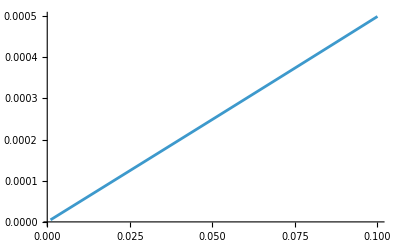

```mathematica
fn=totμmore/.{μ->0.1,v0->0.0004,k0->200};
Plot[fn,{ηx,0.001,0.1}]
```

```mathematica
ex=Simplify[1/(8 π^2 ηx^3 μ)(-π ηx^2 μ 0+(2 √(ηtilde^2-μ^2) (-ηtilde+√(ηtilde^2-ηx^2 μ^2)))/ηtilde 0+ ηx^2 μ ArcCos[μ/ηtilde]0+ 2 ηx μ (EllipticE[ArcSin[ηx],1/ηx^2]+EllipticE[ArcSin[(ηx μ)/ηtilde],1/ηx^2]))]/.rep1
TeXForm[ex]
```

(EllipticE[ArcSin[η_x],1/η_x^2]+EllipticE[ArcSin[(μ η_x)/(η̃)],1/η_x^2])/(4 π^2 η_x^2)

\frac{E\left(\sin ^{-1}\left(\frac{\mu  \eta _x}{\tilde{\eta }}\right)|\frac{1}{\eta _x^2}\right)+E\left(\sin
   ^{-1}\left(\eta _x\right)|\frac{1}{\eta _x^2}\right)}{4 \pi ^2 \eta _x^2}

## Nonlinear 2 for x tilt: only vz Ωx is nonzero

```mathematica
(* -Graphics-;-Graphics-; -Graphics- *)
```

### va Ωa: all zero

```mathematica
(* NO TILT *)
facx(* = 1/D[enx,κ] *)=1/v0;enx=v0 κ;
intg0=FullSimplify[ (k0+κ Cos[γ])/1 facx^2 enx{ v0vecxtilt[[1]] Om[[1]],v0vecxtilt[[2]] Om[[2]], v0vecxtilt[[3]] Om[[3]]}]/.{ηx ->0 ,κ->μ facx}

FullSimplify[Integrate[intg0,{γ,0,π}]+Integrate[intg0,{γ,π,2π}],ass]
```

{-1/4 Cos[γ] Cos[ϕ]^2 Sin[2 γ],-1/2 Cos[γ]^2 Sin[γ] Sin[ϕ]^2,-1/2 Sin[γ]^3}

{0,0,0}

```mathematica
facx(* = 1/D[enx,κ] *)=1/(v0(1+η Cos[γ](* ηx  Cos[ϕ]*)));enx=v0 κ(1+ηx Cos[γ]Cos[ϕ])+ηt Cos[ϕ];
intg=FullSimplify[ (k0+κ Cos[γ])/1 facx^2 enx{ v0vecxtilt[[1]] Om[[1]],v0vecxtilt[[2]] Om[[2]], v0vecxtilt[[3]] Om[[3]]}]/.{ηx ->η/Cos[ϕ] ,κ->(μ-v0 k0 Cos[ϕ])facx}
FullSimplify[Integrate[intg,{γ,0,π},Assumptions->η∈ Reals &&  0<η<=1]+Integrate[intg,{γ,π,2π},Assumptions->η∈ Reals &&  0<η<=1]]
```

{-(v0 Cos[ϕ] ((μ-k0 v0 Cos[ϕ])/(v0 (1+η Cos[γ]))+Cos[ϕ] (k0+(η Cos[γ] (μ-k0 v0 Cos[ϕ]))/(v0 (1+η Cos[γ]) Cos[ϕ]))) (Cos[γ] Cos[ϕ]+η/Cos[ϕ]) Sin[2 γ])/(4 (1+η Cos[γ]) (μ-k0 v0 Cos[ϕ])),-(v0 Cos[γ] ((μ-k0 v0 Cos[ϕ])/(v0 (1+η Cos[γ]))+Cos[ϕ] (k0+(η Cos[γ] (μ-k0 v0 Cos[ϕ]))/(v0 (1+η Cos[γ]) Cos[ϕ]))) Sin[2 γ] Sin[ϕ]^2)/(4 (1+η Cos[γ]) (μ-k0 v0 Cos[ϕ])),-(v0 ((μ-k0 v0 Cos[ϕ])/(v0 (1+η Cos[γ]))+Cos[ϕ] (k0+(η Cos[γ] (μ-k0 v0 Cos[ϕ]))/(v0 (1+η Cos[γ]) Cos[ϕ]))) Sin[γ]^3)/(2 (1+η Cos[γ]) (μ-k0 v0 Cos[ϕ]))}

{0,0,0}

### ϵab va Ωb: only vz Ωx is nonzero

```mathematica
(* NO TILT *)
facx(* = 1/D[enx,κ] *)=1/v0;enx=v0 κ;
intg0=FullSimplify[ (k0+κ Cos[γ])/1 facx^2 enx{ v0vecxtilt[[1]] Om[[2]],v0vecxtilt[[2]] Om[[3]], v0vecxtilt[[3]] Om[[1]]}]/.{ηx ->0 ,κ->μ facx}

FullSimplify[Integrate[intg0,{γ,0,π}]+Integrate[intg0,{γ,π,2π}],ass]
```

{-1/4 Cos[γ] Cos[ϕ] Sin[2 γ] Sin[ϕ],-1/2 Cos[γ] Sin[γ]^2 Sin[ϕ],-1/2 Cos[γ] Cos[ϕ] Sin[γ]^2}

{0,0,0}

```mathematica
facx(* = 1/D[enx,κ] *)=1/(v0(1+η Cos[γ](*Cos[ϕ]*)));enx=v0 κ(1+ηx Cos[γ]Cos[ϕ])+ηt Cos[ϕ];
intg=FullSimplify[ (k0+κ Cos[γ])/1 facx^2 enx{ v0vecxtilt[[1]] Om[[2]],v0vecxtilt[[2]] Om[[3]], v0vecxtilt[[3]] Om[[1]]}]/.{ηx ->η/Cos[ϕ] ,κ->(μ-v0 k0 η)facx}
FullSimplify[Integrate[intg,{γ,0,π},Assumptions->η∈ Reals &&  0<η<=1]+Integrate[intg,{γ,π,2π},Assumptions->η∈ Reals &&  0<η<=1],ass]/.η ->ηx Cos[ϕ]
```

{-(v0 ((-k0 v0 η+μ)/(v0 (1+η Cos[γ]))+Cos[ϕ] (k0+(η (-k0 v0 η+μ) Cos[γ])/(v0 (1+η Cos[γ]) Cos[ϕ]))) (Cos[γ] Cos[ϕ]+η/Cos[ϕ]) Sin[2 γ] Sin[ϕ])/(4 (-k0 v0 η+μ) (1+η Cos[γ])),-(v0 Cos[γ] ((-k0 v0 η+μ)/(v0 (1+η Cos[γ]))+Cos[ϕ] (k0+(η (-k0 v0 η+μ) Cos[γ])/(v0 (1+η Cos[γ]) Cos[ϕ]))) Sin[γ]^2 Sin[ϕ])/(2 (-k0 v0 η+μ) (1+η Cos[γ])),-(v0 Cos[ϕ] ((-k0 v0 η+μ)/(v0 (1+η Cos[γ]))+Cos[ϕ] (k0+(η (-k0 v0 η+μ) Cos[γ])/(v0 (1+η Cos[γ]) Cos[ϕ]))) Sin[γ] Sin[2 γ])/(4 (-k0 v0 η+μ) (1+η Cos[γ]))}

{0,(π (μ+k0 v0 Cos[ϕ]-k0 v0 ηx Cos[ϕ]) (-2+ηx^2 Cos[ϕ]^2-2 ⅈ √(-1+ηx^2 Cos[ϕ]^2)) Sin[ϕ])/(2 ηx^3 (-μ+k0 v0 ηx Cos[ϕ]) Cos[ϕ]^3),(π (μ+k0 v0 Cos[ϕ]-k0 v0 ηx Cos[ϕ]) (-2+ηx^2 Cos[ϕ]^2-2 ⅈ √(-1+ηx^2 Cos[ϕ]^2)))/(2 ηx^3 (-μ+k0 v0 ηx Cos[ϕ]) Cos[ϕ]^2)}

```mathematica
(* only last component is nonzero *)
```

#### performing the nonzero integral for vz Ωx

```mathematica
(* last component, which is nonzero:(π (-μ+k0 v0 (-1+ηx) Cos[ϕ]) (-2+ηx^2 Cos[ϕ]^2-2 ⅈ √(-1+ηx^2 Cos[ϕ]^2)))/(2 ηx^3 (μ-k0 v0 ηx Cos[ϕ]) Cos[ϕ]^2) *)
Clear[int];FullSimplify[((-μ+k0 v0 (-1+ηx) Cos[ϕ]) (-2+ηx^2 Cos[ϕ]^2-2 √(1-ηx^2 Cos[ϕ]^2)))/((μ-k0 v0 ηx Cos[ϕ]) Cos[ϕ]^2)/.{Cos[ϕ]->u,Cos[ϕ]^2->u^2,μ->μt v0 k0 },ass]
```

((2-u^2 ηx^2+2 √(1-u^2 ηx^2)) (u (-1+ηx)-μt))/((u ηx-μt) Cos[ϕ]^2)

```mathematica
((2-u^2 ηx^2+2 √(1-u^2 ηx^2)) (u (-1+ηx)-μt))/((u ηx-μt) Cos[ϕ]^2);
num=Expand[(-μt+ (-1+ηx)u) (-2+ηx^2 u^2-2 sqrt)]
den=  (μt-ηx u)u^2 √(1-u^2);
num=Normal[FullSimplify[Series[num,{u,0,3}]]]/.sqrt->√(1-u^2)
```

2 u+2 sqrt u-2 u ηx-2 sqrt u ηx-u^3 ηx^2+u^3 ηx^3+2 μt+2 sqrt μt-u^2 ηx^2 μt

-2 u (1+√(1-u^2)) (-1+ηx)+u^3 (-1+ηx) ηx^2+2 (1+√(1-u^2)) μt-u^2 ηx^2 μt

```mathematica
ters={(-2 u (1+√(1-u^2)) (-1+ηx)+0 u^3 (-1+ηx) ηx^2+2 (1+√(1-u^2)) μt-0 u^2 ηx^2 μt)/den,(-2 u (1+√(1-u^2)) (-1+ηx)0+u^3 (-1+ηx) ηx^2+2 (1+√(1-u^2)) μt 0-u^2 ηx^2 μt)/den}//FullSimplify
```

{(2 (1+√(1-u^2)) (u (-1+ηx)-μt))/(u^2 √(1-u^2) (u ηx-μt)),(ηx^2 (u-u ηx+μt))/(√(1-u^2) (u ηx-μt))}

```mathematica
FullSimplify[Series[π/(2 ηx^3)ters,{ηx,0,1}]]
```

{(π (1+√(1-u^2)) (u+μt))/(u^2 √(1-u^2) μt ηx^3)+(π (1+1/(√(1-u^2))))/(μt^2 ηx^2)+(π u (1+1/(√(1-u^2))))/(μt^3 ηx)+(π u^2 (1+1/(√(1-u^2))))/μt^4+(π u^3 (1+1/(√(1-u^2))) ηx)/μt^5+O[ηx]^2,-(π (u+μt))/(2 (√(1-u^2) μt) ηx)-(π u^2)/(2 (√(1-u^2) μt^2))-((π u^3) ηx)/(2 (√(1-u^2) μt^3))+O[ηx]^2}

### for μt > ηx

```mathematica
Clear[t];
ass1=Assumptions->{kp,k0,μt,δ,a,v0,kx,ky,ηx}∈ Reals&&    0<ηx<=1&&  μt>0 && μt>ηx;
t[u_]=Simplify[{∫ters[[1]]ⅆu,∫ters[[2]]ⅆu},ass1]
```

{-(2 (μt+√(1-u^2) μt-(2 u ηx ArcTan[(u √(-ηx^2+μt^2))/(u ηx+(-1+√(1-u^2)) μt)])/(√(-ηx^2+μt^2))-2 u Log[-1+√(1-u^2)]+u Log[(-1+√(1-u^2)) (u ηx-μt)]))/(u μt),-2 (-1+ηx) ηx ArcTan[u/(-1+√(1-u^2))]-(2 ηx μt ArcTan[(u √(-ηx^2+μt^2))/(u ηx+(-1+√(1-u^2)) μt)])/(√(-ηx^2+μt^2))}

```mathematica
lowlim=Simplify[Normal[Series[t[-1+δ],{δ,0,2},ass1]]/.δ->0,ass1];
uplimforμtgηx=Simplify[Normal[Series[t[1-δ],{δ,1,0},Assumptions->{μt,ηx}∈ Reals && μt>0 && μt>ηx]]/.δ->0,ass1];
tot1=Simplify[uplimforμtgηx-lowlim,ass1];
tot=FullSimplify[tot1[[1]]+tot1[[2]],ass1]
```

(3 (-4+π (-1+ηx) ηx) μt+(4 ηx (-2+μt^2) (-ArcCot[ηx/(√(-ηx^2+μt^2))]+ArcCot[(ηx+μt)/(√(-ηx^2+μt^2))]))/(√(-ηx^2+μt^2))-2 Log[4]+4 Log[(ηx+μt)/μt])/(2 μt)

```mathematica
totmore[μt_,ηx_]=π/(2 ηx^3)(3 (-4+π (-1+ηx) ηx) μt+(4 ηx (-2+μt^2) (-ArcCot[ηx/(√(-ηx^2+μt^2))]+ArcCot[(ηx+μt)/(√(-ηx^2+μt^2))]))/(√(-ηx^2+μt^2))-2 Log[4]+4 Log[(ηx+μt)/μt])/(2 μt);
```

### for μt < ηx

```mathematica
Clear[tt];
ass2=Assumptions->{kp,k0,μt,δ,a,v0,kx,ky,ηx}∈ Reals&&    0<ηx<=1&&  μt>0 && μt<ηx;
tt[u_]=Simplify[{∫ters[[1]]ⅆu,∫ters[[2]]ⅆu},ass2]
```

{-(2 (μt+√(1-u^2) μt-(2 u ηx ArcTan[(u √(-ηx^2+μt^2))/(u ηx+(-1+√(1-u^2)) μt)])/(√(-ηx^2+μt^2))-2 u Log[-1+√(1-u^2)]+u Log[(-1+√(1-u^2)) (u ηx-μt)]))/(u μt),-2 (-1+ηx) ηx ArcTan[u/(-1+√(1-u^2))]-(2 ηx μt ArcTan[(u √(-ηx^2+μt^2))/(u ηx+(-1+√(1-u^2)) μt)])/(√(-ηx^2+μt^2))}

```mathematica
Simplify[Normal[Series[tt[μt/ηx-δ],{δ,1,0},Assumptions->{μt,ηx}∈ Reals && μt>0 && μt<ηx]]/.δ->0,ass2]
```

{-(2 (μt+(μt √((2 ηx-μt) μt))/ηx+(2 (ηx-μt) ArcTanh[((ηx-μt) √(ηx^2-μt^2))/(ηx^2-μt √(-μt (-2 ηx+μt)))])/(√(ηx^2-μt^2))+(-1+μt/ηx) Log[ηx-√((2 ηx-μt) μt)]+(2 (ηx-μt) (ⅈ π+Log[1-(√((2 ηx-μt) μt))/ηx]))/ηx))/(μt (-1+μt/ηx)),-2 (-1+ηx) ηx ArcTan[(-ηx+μt)/(-ηx+√((2 ηx-μt) μt))]-(2 ηx μt ArcTanh[((ηx-μt) √(ηx^2-μt^2))/(ηx^2-μt √(-μt (-2 ηx+μt)))])/(√(ηx^2-μt^2))}

```mathematica
lowlim=Simplify[Normal[Series[tt[-1+δ],{δ,0,2},ass1]]/.δ->0,ass2];
uplimforμtlηx=Simplify[Normal[Series[tt[μt/ηx-δ],{δ,1,0},Assumptions->{μt,ηx}∈ Reals && μt>0 && μt<ηx]]/.δ->0,ass2];
tot2=Simplify[uplimforμtlηx-lowlim,ass2];
tot=Simplify[tot1[[1]]+tot1[[2]],ass2]
```

1/(2 μt √(-ηx^2+μt^2))(-4 ηx (-2+μt^2) ArcTan[(√(-ηx^2+μt^2))/ηx]+4 ηx (-2+μt^2) ArcTan[(√(-ηx^2+μt^2))/(ηx+μt)]+√(-ηx^2+μt^2) (-12 μt-3 π ηx μt+3 π ηx^2 μt-2 Log[4]-4 Log[μt]+4 Log[ηx+μt]))

```mathematica
totless[μt_,ηx_]=π/(2 ηx^3)1/(2 μt √(-ηx^2+μt^2))(-4 ηx (-2+μt^2) ArcTan[(√(-ηx^2+μt^2))/ηx]+4 ηx (-2+μt^2) ArcTan[(√(-ηx^2+μt^2))/(ηx+μt)]+√(-ηx^2+μt^2) (-12 μt-3 π ηx μt+3 π ηx^2 μt-2 Log[4]-4 Log[μt]+4 Log[ηx+μt]));
```

```mathematica
totμmore[0.1,0]
```

Power::infy: Infinite expression 1/0^3 encountered.

ComplexInfinity

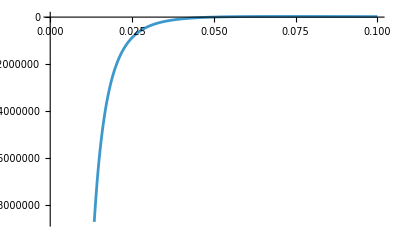

```mathematica
μval=0.1;
Plot[totμmore[μval,ηx],{ηx,0.0001,μval}]
```

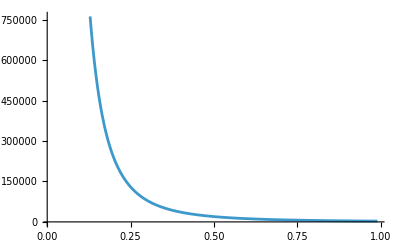

```mathematica
μval=0.01;
Plot[totμless[μval,ηx],{ηx,μval,0.99}]
```

## Nonlinear 1 for z tilt: diagonal ones nonzero

```mathematica
(* -Graphics-;  -Graphics-; -Graphics- *)
```

### taa

```mathematica
-J facz{ v0vecztilt[[1]] Om[[1]], v0vecztilt[[2]] Om[[2]], v0vecztilt[[3]] Om[[3]]}
```

{(Cos[γ] Cos[ϕ]^2 Sin[2 γ])/(4 (1+ηz Sin[γ])),(Cos[γ] Sin[2 γ] Sin[ϕ]^2)/(4 (1+ηz Sin[γ])),(Sin[γ]^2 (ηz+Sin[γ]))/(2 (1+ηz Sin[γ]))}

```mathematica
(*{-(Cos[ϕ]^2 Sin[γ] Cos[γ]^2)/2,-(Sin[ϕ]^2 Sin[γ] Cos[γ]^2)/2,-(η Sin[γ]^2+ Sin[γ]^3)/2}: *)
FullSimplify[2Integrate[{(Cos[ϕ]^2 ttotz[1,2])/(2(2π)^3),(Sin[ϕ]^2 ttotz[1,2])/(2(2π)^3),(ηz ttotz[2,0]+ ttotz[3,0])/(2(2π)^3)},{ϕ,0,π}],ass]
```

{(-2+ηz^2+2 √(1-ηz^2))/(16 π ηz^3),(-2+ηz^2+2 √(1-ηz^2))/(16 π ηz^3),-(-2+ηz^2+2 √(1-ηz^2))/(8 π ηz^3)}

```mathematica
h=(-2+ηz^2+2 √(1-ηz^2))/(16 π ηz^3)/.ηz->Subscript[η, z]//Simplify
TeXForm[h]
```

(-2+η_z^2+2 √(1-η_z^2))/(16 π η_z^3)

\frac{\eta _z^2+2 \sqrt{1-\eta _z^2}-2}{16 \pi  \eta _z^3}

```mathematica
(* -Graphics-; -Graphics-; -Graphics- *)
```

#### Dxy

```mathematica
int= J facz v0vecztilt[[1]] Om[[2]]/.repkz
(-Cos[γ] Cos[ϕ] 2Sin[γ]Cos[γ] Sin[ϕ])/4//Expand
-1/2  Cos[ϕ] Sin[ϕ]ttotz[1,2]
```

-(Cos[γ] Cos[ϕ] Sin[2 γ] Sin[ϕ])/(4 (1+ηz Sin[γ]))

-1/2 Cos[γ]^2 Cos[ϕ] Sin[γ] Sin[ϕ]

-(π (-2+ηz^2+2 √(1-ηz^2)) Cos[ϕ] Sin[ϕ])/(2 ηz^3)

```mathematica
(* this gives zero *)
```

#### Dyz

```mathematica
int=J facz v0vecztilt[[2]] Om[[3]]/.repkz
(-Sin[ϕ])/2 ttotz[2,1]
```

-(Cos[γ] Sin[γ]^2 Sin[ϕ])/(2 (1+ηz Sin[γ]))

0

#### Dzx

```mathematica
int=J facz v0vecztilt[[3]] Om[[1]]/.repkz
(-Cos[ϕ] (η+Sin[γ]) 2Sin[ γ]Cos[γ])/4//Expand
-1/2 η Cos[ϕ]ttotz[1,1]-1/2 Cos[ϕ]ttotz[2,1]
```

-(Cos[ϕ] (ηz+Sin[γ]) Sin[2 γ])/(4 (1+ηz Sin[γ]))

-1/2 η Cos[γ] Cos[ϕ] Sin[γ]-1/2 Cos[γ] Cos[ϕ] Sin[γ]^2

0

## Nonlinear 2 for z tilt

### va Ωa

```mathematica
facz(* = 1/D[enz,κ] *)=1/(v0 (1+ηz Sin[γ]));enz=v0 κ(1+ηz  Sin[γ]);intg=Simplify[2(* two-factor to make Mathematica to do the integral*) (k0+κ Cos[γ])/1 facz^2 enz{ v0vecztilt[[1]] Om[[1]],v0vecztilt[[2]] Om[[2]], v0vecztilt[[3]] Om[[3]]}]/.{κ->μ facz}
```

{-(Cos[γ]^2 Cos[ϕ]^2 Sin[γ])/(1+ηz Sin[γ]),-(Cos[γ]^2 Sin[γ] Sin[ϕ]^2)/(1+ηz Sin[γ]),-(Sin[γ]^2 (ηz+Sin[γ]))/(1+ηz Sin[γ])}

```mathematica
i1=Integrate[intg,{γ,0,π},Assumptions->{ηz,ϕ}∈ Reals &&  0<ηz<=1];
i2=Integrate[intg,{γ,π,2π},Assumptions->{ηz,ϕ}∈ Reals &&  0<ηz<=1];
itot=1/2 FullSimplify[i1+i2,ass]
```

{-(π (-2+ηz^2+2 √(1-ηz^2)) Cos[ϕ]^2)/(2 ηz^3),-(π (-2+ηz^2+2 √(1-ηz^2)) Sin[ϕ]^2)/(2 ηz^3),(π (-2+ηz^2+2 √(1-ηz^2)))/(2 ηz^3)}

### ϵab va Ωb

```mathematica
facz(* = 1/D[enz,κ] *)=1/(v0 (1+ηz Sin[γ]));enz=v0 κ(1+ηz  Sin[γ]);intg=Simplify[2(* two-factor to make Mathematica to do the integral*) (k0+κ Cos[γ])/1 facz^2 enz{ v0vecztilt[[1]] Om[[2]],v0vecztilt[[2]] Om[[3]], v0vecztilt[[3]] Om[[1]]}]/.{κ->μ facz}
```

{-(Cos[γ]^2 Cos[ϕ] Sin[γ] Sin[ϕ])/(1+ηz Sin[γ]),-(Cos[γ] Sin[γ]^2 Sin[ϕ])/(1+ηz Sin[γ]),-(Cos[γ] Cos[ϕ] Sin[γ] (ηz+Sin[γ]))/(1+ηz Sin[γ])}

```mathematica
i1=Integrate[intg,{γ,0,π},Assumptions->{ηz,ϕ}∈ Reals &&  0<ηz<=1];
i2=Integrate[intg,{γ,π,2π},Assumptions->{ηz,ϕ}∈ Reals &&  0<ηz<=1];
itot=1/2 FullSimplify[i1+i2,ass]
```

{-(π (-2+ηz^2+2 √(1-ηz^2)) Cos[ϕ] Sin[ϕ])/(2 ηz^3),0,0}

```mathematica
(* it is zero *)
```